# < Automated Acute Leukemia Symptom Analysis from Microscopical Blood Images >

<Junseo Park>

<Eryn Gillam>

## Description

Acute Lymphoblastic Leukemia (ALL), or Acute Lymphocytic Leukemia is a type of cancer of the blood and bone marrow that affects white blood cells. The diagnosis of ALL is done through several steps, but one step that causes errors is looking through the peripheral blood slides to find blast cells, which are symptoms of blood cancer. Using image processing and machine learning, images of peripheral blood slides were analyzed. Image processing was used to pick out the lymphoblasts. Specifically, color related functions were used because the lymphoblasts have a very dark purple color that stands out in a peripheral blood slide image. A classifier was trained and tested to distinguish blast cells and non-blast cells.

# Refining the Data for Training/Testing of Machine Learning

Function refinedimg detects the color with the least green value in the microscopical blood image.

```mathematica
refinedimg[image_]:= 
Module[
{dominantcolors,detectedcolors,refinedimage,dominantcolor
},
dominantcolors=DominantColors[image];
dominantcolor=SortBy[dominantcolors,#[[2]]&][[1]];
detectedcolors=ColorDetect[image,dominantcolor];
(*Erosion was used to erase the noise on the image that comes from ColorDetect*)
refinedimage=Erosion[Binarize[ImageAdjust[detectedcolors],0.6],3];
{image,refinedimage}
]
```

```mathematica
refinedimg[-Graphics-]
```

{-Graphics-,-Graphics-}

Example of an error case of refinedimg.

```mathematica
-Graphics-;
```

The error above occurred due a significant area of the microscopical blood image being as purple as the lymphoblasts. The refineimg2 is different from refinedimg; the function takes the results from refinedimg and checks for the error using Component Measurements. refineimg2 creates a result by choosing the dominant color in the image that is below a fixed green value of 0.4.

```mathematica
refinedimg2[list_]:=
Module[{images2,dominantcolors,detectedcolors,refinedimage,originalimg,images
},
originalimg=list[[1]];
images=list[[2]];
images2=Select[images,Length[ComponentMeasurements[#,"Image"]]≤100&];
{originalimg,If[Length[images2]≠1,
dominantcolors=Select[DominantColors[originalimg],#[[2]]≤0.4&];
detectedcolors=ColorDetect[originalimg,#]&/@dominantcolors;
(*  *)
refinedimage=Erosion[Dilation[ImageAdjust[#],0.6],3]&/@detectedcolors;
Select[refinedimage,Length[ComponentMeasurements[#,"Image"]]≤100&]
,
Erosion[Binarize[ImageAdjust[#],0.6],3]&/@images2]}
]
```

Function refinetheimage combines refinedimg and refineimg2.

```mathematica
refinetheimage[image_,dilationparameter_:1]:=Module[
{result},
result=refinedimg2[refinedimg[image,dilationparameter]]
]
```

Function pickcomponent takes the result from refinetheimage and chooses components that are not adjacent to the border of the image and is not smaller than a certain area threshold. Coordinates of the component are then expanded and used to trim those coordinates from the original image.

```mathematica
pickcomponent[input_,coordinateparameter_:15,areaparameter_:3000]:=Module[
{components,blasts,blastcoordinates,coordinates,originalimage,refinedimage,onecoordinate,onecoordinates
},
originalimage=input[[1]];
refinedimage=input[[2]];
components=ComponentMeasurements[refinedimage,{"Image","AdjacentBorders","Area","PerimeterLength","BoundingBoxArea","BoundingBox"},#Area>50&&#AdjacentBorders=={}&];
If[Length[components]≠1,
blasts=Select[components,#[[2,2]]=={}&&#[[2,3]]≥areaparameter&];
blastcoordinates=#[[2,-1]]&/@blasts;
coordinates=Map[{{#[[1,1]]-coordinateparameter,#[[1,2]]-coordinateparameter},{#[[2,1]]+coordinateparameter,#[[2,2]]+coordinateparameter}}&,blastcoordinates];
ImageTrim[originalimage,#]&/@coordinates
,
onecoordinate=components[[1,2,-1]];
onecoordinates={{onecoordinate[[1,1]]-coordinateparameter,onecoordinate[[1,2]]-coordinateparameter},{onecoordinate[[2,1]]+coordinateparameter,onecoordinate[[2,2]]+coordinateparameter}};
ImageTrim[originalimage,onecoordinates]
]]
```

By default, 15 is used for the coordinateparameter and 3000 is used for the area parameter. Coordinate parameter is the number by which the original coordinates are expanded by. Area Parameter is the threshold area and all components with an area above it are selected. 3000 is an approximation of where the area of the lymphoblasts and the noise are separated.

# Machine Learning

To create classifiers for the data, the function randomclassifier was created. The function takes a random seed and develops a classifier w/ 80% of the data used for train, returning the classifier measurements analysis from 20% of the data. The train data and test data are separated by using RandomSample. In order to normalize the accuracy, the function was used 100 times. 80% of the dataset was used to train the classifier and the other 20% was used to test it.

```mathematica
randomclassifier[seednum_]:= 
Module[{blaststest,blaststrain,notblaststrain,notblaststest,classifier,notblastcomplement,blastcomplement,cm,testdata,results},
RandomSeed[seednum];
blaststrain=RandomSample[blastcelltrain,Length[blast]*0.8];
notblaststrain=RandomSample[notblastcelltrain,Length[notblast]*0.8];
blastcomplement=Complement[blast,blaststrain];
blaststest=Map[#->"Blast Cell"&,blastcomplement];
notblastcomplement=Complement[notblast,notblaststrain];
notblaststest=Map[#->"Not Blast Cells"&,notblastcomplement];
classifier=Classify[<|"Blast Cell"->blaststrain,"Not Blast Cells"->notblaststrain|>];
testdata=Flatten[{blaststest,notblaststest}];
cm=ClassifierMeasurements[classifier,testdata];
results=Grid[{#,cm[#]}&/@cm["Properties"],Frame->All];
{results,classifier}]
```

Below is a sample classifier and a sample confusion matrix plot. The average accuracy of the 100 classifiers made is 98.1%. The standard deviation of the accuracy was 2.1%.

```mathematica
classifiersample=ClassifierFunction[…];
```

```mathematica
classifiersample[-Graphics-]
```

Not Blast Cells

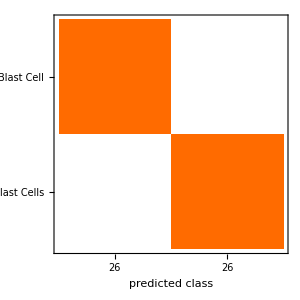
```mathematica
-Graphics-;
```

# Extracting Features from the Complete Pictures of Blood

In order to analyze complete slide, the method for image analysis needed to be changed. The function find does the same as refinedimg, but is made to work on the full blood peripheral slide images like the one provided above.

Function find used with Dilationparameter of 1 because normally, the image doesn't need to be dilated. Erosionparameter is 3 because erosion gets rid of the noise in the image

```mathematica
find[image_,dilationparameter_:1,binarizeparameter_:0.6,erosionparameter_:3]:= 
Module[
{dominantcolors,detectedcolors,refinedimage,dominantcolor},
dominantcolors=DominantColors[image];
dominantcolor=SortBy[dominantcolors,#[[2]]&][[1]];
detectedcolors=ColorDetect[image,dominantcolor];
refinedimage=Erosion[Dilation[Binarize[ImageAdjust[detectedcolors],binarizeparameter],dilationparameter],erosionparameter];
{image,refinedimage,dominantcolor}
]
```

Outcome of find

```mathematica
find[sampleimg]
```

{-Graphics-,-Graphics-,RGBColor[0.26206393975885867, 0.06829076026263817, 0.4140928737525335]}

select is similar to the pickcomponent function. This function is different in that it gives the center coordinates of each component and is made to work on the full blood peripheral slide images like the one provided above.

```mathematica
select[input_,coordinateparameter_:30,areaparameter_:3000]:=
Module[
{components,blasts,blastcoordinates,coordinates,originalimage,refinedimage},
originalimage=input[[1]];
refinedimage=input[[2]];
components=ComponentMeasurements[refinedimage,{"Image","AdjacentBorders","Area","PerimeterLength","BoundingBoxArea","BoundingBox"},#Area>areaparameter&&#AdjacentBorders=={}&];
blastcoordinates=#[[2,-1]]&/@components;
coordinates=Map[{{#[[1,1]]-coordinateparameter,#[[1,2]]-coordinateparameter},{#[[2,1]]+coordinateparameter,#[[2,2]]+coordinateparameter}}&,blastcoordinates];
{ImageTrim[originalimage,#],Flatten[{Mean[#[[All,1]]],Mean[#[[All,2]]]}]}&/@coordinates
]
```

Outcome of select

```mathematica
select[find[sampleimg]]
```

{{-Graphics-,{747.,926.5}},{-Graphics-,{1071.5,316.5}}}

overall combines find and select and shows the results as a grid

```mathematica
overall[image_]:=
Module[
{result1,result2,result3,classifiedresults},
result1=find[image];
result2=select[result1[[1;;2]]];
classifiedresults=classifiersample[#[[1]]]&/@result2;
result3=Grid[Prepend[Partition[Flatten[Riffle[result2,classifiedresults],1],3],{"Detected Lymphoblast","Coordinates of the  Center","Classified"}],Frame->All];
{image,result3}
]
```

These are the results provided for 5 images of healthy patients. When the algorithm was tested on 59 blood images of healthy patients, the algorithm picked out all the lymphoblasts and classified all of them as “Not Blast Cells”.

Outcome of overall

```mathematica
Column[overall[#]&/@bloodwoblast]
```

{-Graphics-,Detected Lymphoblast | Coordinates of the  Center | Classified
-Graphics- | {681.5,1209.5} | Not Blast Cells
-Graphics- | {1971.,483.5} | Not Blast Cells}
{-Graphics-,Detected Lymphoblast | Coordinates of the  Center | Classified
-Graphics- | {895.,1265.} | Not Blast Cells
-Graphics- | {1768.5,1106.5} | Not Blast Cells}
{-Graphics-,Detected Lymphoblast | Coordinates of the  Center | Classified
-Graphics- | {651.,1330.} | Not Blast Cells
-Graphics- | {436.,1266.5} | Not Blast Cells
-Graphics- | {1386.5,1167.} | Not Blast Cells}
{-Graphics-,Detected Lymphoblast | Coordinates of the  Center | Classified
-Graphics- | {446.,1191.5} | Not Blast Cells
-Graphics- | {2026.,1048.} | Not Blast Cells}
{-Graphics-,Detected Lymphoblast | Coordinates of the  Center | Classified
-Graphics- | {1791.,1395.5} | Not Blast Cells
-Graphics- | {838.,1243.5} | Not Blast Cells
-Graphics- | {104.,653.} | Not Blast Cells
-Graphics- | {875.,622.5} | Not Blast Cells}

#### Conclusion

The original purpose of this project was to diagnose ALL from blood images. However, due to the lack of sufficient data from one specific patient, it was only possible to create a program which analyzes individual blood smear images. It was found that both the classifier and supporting functions were quite applicable for the purpose, with the classifier having an accuracy measure of 98.1%.Therefore, it should be expected that by expanding the image dataset to that of a full slide, a comprehensive analysis on ALL and blast cells will be possible. Also, as shown below, peripheral blood smear images available for this project that contain blast cells had labelling which caused several errors in the algorithm. In contrast, when the algorithm was tested on 59 blood images of healthy patients, the algorithm identified all of the lymphoblasts through image processing and had a 100% accuracy in classifying the lymphoblasts as non-blast cells.

```mathematica
bloodwblast[[1]]
```

-Graphics-

#### Future Works

In order to improve the project, data collection from local hospitals will be conducted. Here, I plan to obtain pictures of the entire blood slide of each patient, so that my project can be extended to diagnosis of the disease. Also, I will obtain original images of peripheral blood smears of patients with ALL to test my algorithm, since the images I obtained from ALL-IDB came with labels. Peripheral blood smears of patients without ALL will also be acquired to get a more Further, I will apply the algorithm to not only patients with ALL but also those who have AML and MDS, which are types of blood cancer.

#### Acknowledgements

I acknowledge Dr. Fabio Scotti from the University of Milan for providing me with the dataset to work on. 
I acknowledge my mentor Eryn Gillam for providing me with ideas about what to code in order to solve this problem and revising my presentation script & this document.